# Min number of patients

```mathematica
MeanNonResponseVolumeChange=20;
StandardDeviationOfVolumeChange=30;
GroupOfResponses[samplesize_,treatmenteffect_]:=RandomVariate[NormalDistribution[MeanNonResponseVolumeChange+treatmenteffect,StandardDeviationOfVolumeChange],samplesize]
```

```mathematica
ManyNonResponders=GroupOfResponses[200,0];
```

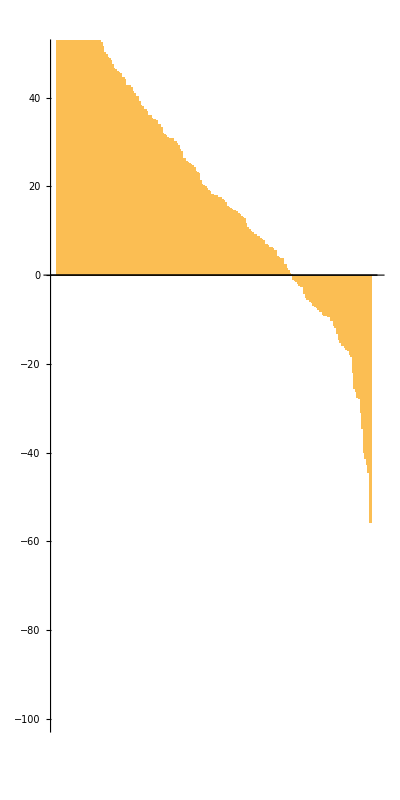

```mathematica
BarChart[Reverse[Sort[ManyNonResponders]],PlotRange->{-100,50},AspectRatio->2,ImageSize->{{250},{250}}]
```

```mathematica
(* treatment effect of '0' corresponds to 5% rate of Objective Response *)
ManyNonResponders=GroupOfResponses[100000,0];
Length[Select[ManyNonResponders,#<-30&]]/Length[ManyNonResponders]//N
```

0.04715

```mathematica
(* 30% rate of Objective Response (volume change below -30%) with treatment effect of -34 *)
ManyResponders=GroupOfResponses[100000,-34];
Length[Select[ManyResponders,#<-30&]]/Length[ManyResponders]//N
ManyResponders=GroupOfResponses[200,-34];
```

0.29801

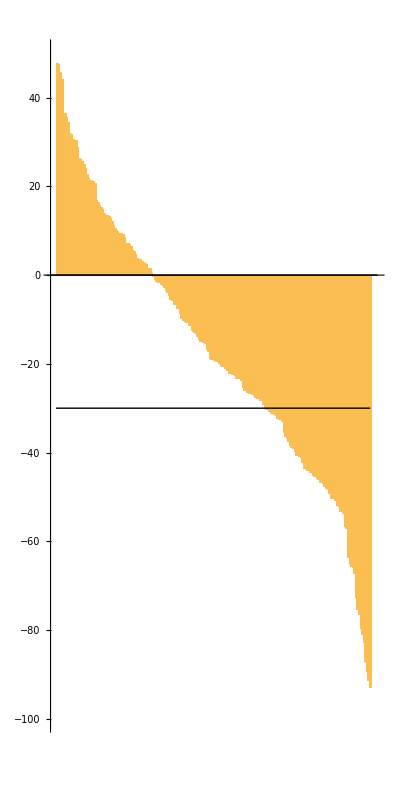

```mathematica
BarChart[Reverse[Sort[ManyResponders]],PlotRange->{-100,50},AspectRatio->2,Epilog->{Black,Line[{{0,-30},{200,-30}}]}]
```

```mathematica
(* Simon Two Stage Design population sizes with 80% Power, 10% type 1 error rate (one-sided), response rate for bad drug p0 = 10%, response rate for good drug p1 = 30%*)
Nstage1=7;
Nstage2=18;

(* number of responses required *)
ResponsesStage1=1;
ResponsesStage2=4;
```

```mathematica
TotalNumberOfTumorSubtypes=10;
NumberOfResponsiveSubtypes=1;
NumberOfNonResponsiveSubtypes=TotalNumberOfTumorSubtypes-NumberOfResponsiveSubtypes;
```

## Min num of patients assessment

```mathematica
Stage1ResponsesInGroups[treatmenteffect_]:=Join[
(* responding groups *)Table[GroupOfResponses[Nstage1,treatmenteffect],{NumberOfResponsiveSubtypes}],
(* non-responding groups *)Table[GroupOfResponses[Nstage1,0],{NumberOfNonResponsiveSubtypes}]
]
```

```mathematica
VolumeThresholdForResponse=-30;

SimonStage1Assessment[listofvolumes_]:=
Length[Select[listofvolumes,#<=VolumeThresholdForResponse&]]
```

```mathematica
Map[SimonStage1Assessment,Stage1ResponsesInGroups[-40]]
```

{3,0,1,1,0,0,0,0,0,0}

```mathematica
ManySimonStage1Assessments[numberofsimulations_,treatmenteffect_]:=Table[Map[SimonStage1Assessment,Stage1ResponsesInGroups[treatmenteffect]],{numberofsimulations}]
```

```mathematica
SimonStage1Power[numberofsimulations_,treatmenteffect_]:=Module[{},
SimulatedTrialAssessments=ManySimonStage1Assessments[numberofsimulations,treatmenteffect];

TrialsThatShouldBePositive=SimulatedTrialAssessments⟦All,1;;NumberOfResponsiveSubtypes⟧;

{TrialsThatShouldBePositive}
]
```

```mathematica
SimonStage1Power[1000,-40]//N
```

{{{3.},{3.},{3.},{3.},{3.},{2.},{4.},{5.},{2.},{0.},{4.},{2.},{4.},{4.},{2.},{3.},{5.},{7.},{1.},{3.},{3.},{4.},{2.},{6.},{2.},{3.},{3.},{3.},{4.},{3.},{4.},{4.},{2.},{2.},{2.},{2.},{2.},{3.},{1.},{1.},{2.},{1.},{4.},{2.},{2.},{3.},{3.},{3.},{1.},{3.},{4.},{4.},{1.},{4.},{3.},{4.},{2.},{3.},{5.},{5.},{1.},{1.},{2.},{4.},{4.},{2.},{1.},{1.},{1.},{3.},{1.},{2.},{4.},{2.},{4.},{2.},{3.},{2.},{0.},{3.},{1.},{4.},{2.},{5.},{3.},{1.},{2.},{4.},{3.},{4.},{4.},{2.},{3.},{1.},{2.},{0.},{1.},{3.},{4.},{3.},{2.},{3.},{4.},{2.},{2.},{3.},{4.},{2.},{1.},{3.},{1.},{1.},{3.},{3.},{7.},{1.},{5.},{4.},{3.},{1.},{3.},{2.},{3.},{1.},{3.},{3.},{1.},{4.},{1.},{2.},{3.},{1.},{3.},{2.},{1.},{2.},{2.},{4.},{3.},{4.},{1.},{5.},{3.},{1.},{5.},{4.},{4.},{4.},{6.},{5.},{2.},{4.},{2.},{3.},{3.},{3.},{4.},{4.},{3.},{2.},{2.},{1.},{2.},{2.},{2.},{3.},{1.},{3.},{4.},{2.},{3.},{4.},{0.},{5.},{1.},{4.},{1.},{4.},{5.},{3.},{2.},{2.},{1.},{3.},{5.},{4.},{1.},{4.},{1.},{4.},{4.},{3.},{2.},{1.},{3.},{2.},{4.},{5.},{3.},{2.},{0.},{1.},{4.},{3.},{4.},{4.},{3.},{3.},{2.},{5.},{4.},{1.},{2.},{4.},{3.},{2.},{2.},{1.},{0.},{3.},{2.},{3.},{4.},{2.},{2.},{5.},{3.},{2.},{1.},{1.},{1.},{3.},{3.},{3.},{2.},{2.},{4.},{4.},{4.},{2.},{2.},{3.},{2.},{2.},{3.},{4.},{1.},{3.},{2.},{1.},{3.},{4.},{4.},{3.},{1.},{2.},{2.},{4.},{2.},{2.},{3.},{2.},{5.},{3.},{4.},{3.},{1.},{4.},{3.},{3.},{1.},{2.},{5.},{2.},{1.},{4.},{3.},{3.},{5.},{2.},{2.},{0.},{2.},{4.},{3.},{2.},{0.},{3.},{1.},{2.},{3.},{3.},{0.},{2.},{2.},{5.},{5.},{3.},{1.},{2.},{1.},{2.},{3.},{2.},{3.},{2.},{3.},{2.},{2.},{0.},{4.},{3.},{1.},{3.},{2.},{3.},{2.},{3.},{4.},{5.},{1.},{3.},{0.},{1.},{1.},{2.},{0.},{3.},{1.},{3.},{2.},{1.},{2.},{3.},{3.},{1.},{2.},{4.},{4.},{3.},{3.},{2.},{4.},{4.},{1.},{2.},{4.},{6.},{1.},{2.},{5.},{5.},{5.},{3.},{3.},{0.},{5.},{0.},{2.},{2.},{4.},{3.},{2.},{3.},{2.},{2.},{3.},{5.},{2.},{2.},{2.},{2.},{4.},{1.},{4.},{2.},{1.},{4.},{0.},{2.},{4.},{2.},{1.},{3.},{3.},{3.},{2.},{3.},{5.},{5.},{4.},{3.},{3.},{2.},{4.},{3.},{2.},{2.},{2.},{2.},{1.},{2.},{2.},{3.},{2.},{2.},{4.},{0.},{5.},{5.},{5.},{2.},{2.},{3.},{1.},{4.},{3.},{5.},{4.},{1.},{3.},{1.},{3.},{2.},{1.},{2.},{1.},{4.},{3.},{5.},{2.},{2.},{5.},{1.},{1.},{1.},{3.},{3.},{3.},{2.},{3.},{4.},{2.},{2.},{4.},{2.},{3.},{3.},{2.},{1.},{0.},{1.},{2.},{2.},{3.},{1.},{4.},{1.},{3.},{2.},{2.},{3.},{3.},{3.},{3.},{3.},{1.},{3.},{3.},{1.},{2.},{1.},{5.},{6.},{4.},{4.},{3.},{2.},{4.},{2.},{2.},{3.},{1.},{2.},{4.},{3.},{1.},{5.},{1.},{3.},{1.},{4.},{2.},{5.},{3.},{0.},{1.},{3.},{3.},{3.},{1.},{0.},{2.},{0.},{2.},{5.},{2.},{4.},{4.},{4.},{4.},{5.},{3.},{2.},{4.},{0.},{1.},{3.},{2.},{2.},{2.},{3.},{1.},{2.},{3.},{4.},{0.},{3.},{5.},{4.},{2.},{1.},{4.},{2.},{2.},{3.},{0.},{5.},{2.},{3.},{1.},{3.},{3.},{4.},{2.},{0.},{2.},{4.},{4.},{3.},{1.},{3.},{1.},{2.},{4.},{4.},{4.},{6.},{2.},{2.},{1.},{3.},{2.},{3.},{2.},{4.},{3.},{2.},{2.},{4.},{2.},{4.},{1.},{1.},{3.},{2.},{5.},{1.},{4.},{1.},{3.},{3.},{1.},{2.},{3.},{2.},{4.},{2.},{5.},{4.},{1.},{3.},{2.},{1.},{6.},{2.},{6.},{0.},{3.},{2.},{2.},{1.},{2.},{2.},{4.},{3.},{2.},{4.},{3.},{2.},{3.},{4.},{0.},{2.},{3.},{1.},{2.},{3.},{3.},{3.},{0.},{2.},{2.},{2.},{2.},{5.},{3.},{4.},{5.},{3.},{2.},{3.},{2.},{6.},{1.},{3.},{1.},{2.},{3.},{1.},{4.},{1.},{5.},{2.},{5.},{2.},{2.},{3.},{4.},{2.},{3.},{6.},{3.},{4.},{1.},{4.},{3.},{4.},{3.},{4.},{3.},{2.},{3.},{4.},{4.},{1.},{1.},{3.},{3.},{3.},{3.},{3.},{3.},{3.},{3.},{4.},{1.},{0.},{3.},{4.},{3.},{0.},{1.},{6.},{1.},{5.},{2.},{4.},{4.},{2.},{0.},{1.},{2.},{2.},{3.},{3.},{4.},{3.},{2.},{4.},{2.},{0.},{3.},{1.},{5.},{2.},{6.},{1.},{1.},{2.},{2.},{2.},{1.},{5.},{2.},{5.},{2.},{2.},{2.},{5.},{2.},{1.},{3.},{3.},{3.},{2.},{3.},{4.},{3.},{4.},{1.},{1.},{1.},{3.},{3.},{3.},{1.},{4.},{3.},{3.},{4.},{1.},{2.},{1.},{3.},{2.},{3.},{3.},{3.},{4.},{1.},{2.},{0.},{2.},{2.},{1.},{3.},{3.},{3.},{5.},{1.},{3.},{2.},{4.},{2.},{1.},{3.},{2.},{3.},{2.},{2.},{5.},{2.},{4.},{1.},{3.},{4.},{4.},{3.},{4.},{3.},{3.},{4.},{3.},{3.},{1.},{4.},{1.},{4.},{1.},{2.},{3.},{3.},{3.},{1.},{3.},{2.},{3.},{4.},{2.},{1.},{1.},{5.},{4.},{3.},{0.},{4.},{3.},{1.},{5.},{2.},{2.},{5.},{2.},{3.},{2.},{2.},{4.},{1.},{2.},{5.},{1.},{3.},{5.},{2.},{4.},{1.},{3.},{2.},{3.},{3.},{1.},{5.},{3.},{4.},{2.},{3.},{2.},{1.},{3.},{3.},{3.},{2.},{2.},{4.},{4.},{4.},{0.},{5.},{2.},{0.},{3.},{2.},{4.},{3.},{3.},{3.},{4.},{2.},{1.},{3.},{1.},{1.},{3.},{1.},{3.},{1.},{1.},{4.},{1.},{1.},{2.},{4.},{3.},{3.},{1.},{1.},{2.},{2.},{0.},{3.},{4.},{5.},{3.},{3.},{3.},{4.},{4.},{2.},{3.},{3.},{2.},{3.},{2.},{4.},{3.},{2.},{1.},{2.},{4.},{1.},{3.},{5.},{3.},{1.},{3.},{2.},{5.},{2.},{0.},{3.},{0.},{0.},{4.},{5.},{4.},{4.},{4.},{2.},{0.},{2.},{1.},{5.},{2.},{2.},{3.},{3.},{4.},{2.},{2.},{3.},{1.},{5.},{6.},{2.},{3.},{2.},{3.},{4.},{2.},{4.},{2.},{0.},{3.},{2.},{4.},{3.},{1.},{1.},{4.},{3.},{3.},{3.},{2.},{4.},{4.},{2.},{3.},{3.},{2.},{5.},{3.},{2.},{4.},{3.},{5.},{1.},{2.},{3.},{2.},{5.},{2.},{3.},{2.},{2.},{2.},{2.},{1.},{3.},{5.},{3.},{5.},{3.},{1.},{3.},{3.},{2.},{1.},{0.},{2.},{2.},{1.},{3.},{3.},{2.},{5.},{2.},{6.},{5.},{1.}}}

```mathematica
SimonStage1PowerAndErrorRateVSEffect=Table[Flatten[{treatmenteffect,SimonStage1Power[10000,treatmenteffect]}],{treatmenteffect,-60,0,1}];
```

```mathematica
Dimensions[SimonStage1PowerAndErrorRateVSEffect]
```

{61,10001}

```mathematica
SimonStage1PowerAndErrorRateVSEffect=Table[Flatten[{treatmenteffect,SimonStage1Power[10,treatmenteffect]}],{treatmenteffect,-60,0,1}];
```

```mathematica
sims=10
Table[SimonStage1PowerAndErrorRateVSEffect[i,Mean[Range[2,10]]], {i, 0, sims}]
```

10

{{{-60,5,5,4,4,5,5,4,5,7,5},{-59,6,6,3,2,4,5,4,6,6,4},{-58,5,6,4,2,6,3,4,5,5,2},{-57,5,5,3,4,3,5,4,2,4,4},{-56,4,7,4,2,4,6,5,5,6,5},{-55,4,3,3,2,5,5,4,3,3,5},{-54,3,5,4,5,3,5,1,4,5,5},{-53,4,5,5,5,5,6,2,5,3,3},{-52,4,5,4,5,4,5,2,4,6,5},{-51,5,0,4,2,4,4,6,5,3,4},{-50,4,3,4,3,5,5,5,3,4,1},{-49,2,3,4,6,1,3,2,4,2,4},{-48,1,3,4,4,2,3,4,5,6,3},{-47,3,2,4,1,2,4,4,4,1,4},{-46,2,6,3,3,2,1,2,3,2,4},{-45,2,4,5,3,3,4,5,4,3,3},{-44,4,1,3,3,1,1,4,3,3,4},{-43,0,5,6,3,4,3,5,3,4,6},{-42,1,1,5,4,4,4,1,2,3,2},{-41,0,3,3,5,5,1,3,1,5,3},{-40,1,3,2,1,4,3,3,2,1,4},{-39,2,3,2,0,3,4,5,1,3,3},{-38,3,1,2,5,2,3,3,3,3,3},{-37,2,4,2,2,3,0,2,4,1,3},{-36,2,2,2,2,3,2,4,3,3,0},{-35,1,0,2,1,1,3,2,4,1,2},{-34,2,2,4,1,3,3,3,1,3,2},{-33,2,1,0,3,1,3,0,2,3,5},{-32,1,0,4,0,1,0,0,1,2,1},{-31,2,2,1,1,1,2,1,3,0,4},{-30,1,1,3,1,1,1,2,3,1,2},{-29,2,0,3,2,0,1,1,0,3,1},{-28,4,1,4,2,0,0,4,1,0,0},{-27,3,2,1,2,1,2,2,1,0,1},{-26,2,2,3,1,1,3,2,2,1,4},{-25,1,2,1,0,2,3,1,1,1,1},{-24,1,2,1,1,1,1,2,2,1,1},{-23,0,1,1,2,3,0,3,2,1,0},{-22,1,0,2,1,1,0,1,3,1,2},{-21,0,1,1,2,1,1,1,2,0,1},{-20,0,2,0,0,1,1,2,0,0,3},{-19,2,2,1,2,0,3,2,0,0,2},{-18,1,2,0,0,1,3,0,1,0,2},{-17,0,1,0,2,2,1,3,0,0,2},{-16,1,0,1,2,0,0,0,1,1,2},{-15,0,1,2,1,0,0,0,0,2,1},{-14,1,1,2,0,1,0,0,0,1,0},{-13,2,1,1,2,1,2,0,0,0,1},{-12,0,0,1,2,1,0,1,1,2,1},{-11,0,1,2,1,2,1,1,0,2,2},{-10,0,1,0,0,0,0,5,1,0,0},{-9,1,1,0,1,1,1,1,2,0,0},{-8,0,1,0,0,1,0,0,0,1,2},{-7,1,0,1,0,1,0,1,1,0,0},{-6,0,0,0,0,1,0,0,1,1,0},{-5,1,0,0,0,0,0,1,0,0,0},{-4,0,0,1,2,1,0,0,0,0,0},{-3,1,0,0,0,2,1,0,0,0,0},{-2,0,1,0,0,0,0,1,1,0,2},{-1,2,0,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,0,0,0,1,0}}[0,6],{{-60,5,5,4,4,5,5,4,5,7,5},{-59,6,6,3,2,4,5,4,6,6,4},{-58,5,6,4,2,6,3,4,5,5,2},{-57,5,5,3,4,3,5,4,2,4,4},{-56,4,7,4,2,4,6,5,5,6,5},{-55,4,3,3,2,5,5,4,3,3,5},{-54,3,5,4,5,3,5,1,4,5,5},{-53,4,5,5,5,5,6,2,5,3,3},{-52,4,5,4,5,4,5,2,4,6,5},{-51,5,0,4,2,4,4,6,5,3,4},{-50,4,3,4,3,5,5,5,3,4,1},{-49,2,3,4,6,1,3,2,4,2,4},{-48,1,3,4,4,2,3,4,5,6,3},{-47,3,2,4,1,2,4,4,4,1,4},{-46,2,6,3,3,2,1,2,3,2,4},{-45,2,4,5,3,3,4,5,4,3,3},{-44,4,1,3,3,1,1,4,3,3,4},{-43,0,5,6,3,4,3,5,3,4,6},{-42,1,1,5,4,4,4,1,2,3,2},{-41,0,3,3,5,5,1,3,1,5,3},{-40,1,3,2,1,4,3,3,2,1,4},{-39,2,3,2,0,3,4,5,1,3,3},{-38,3,1,2,5,2,3,3,3,3,3},{-37,2,4,2,2,3,0,2,4,1,3},{-36,2,2,2,2,3,2,4,3,3,0},{-35,1,0,2,1,1,3,2,4,1,2},{-34,2,2,4,1,3,3,3,1,3,2},{-33,2,1,0,3,1,3,0,2,3,5},{-32,1,0,4,0,1,0,0,1,2,1},{-31,2,2,1,1,1,2,1,3,0,4},{-30,1,1,3,1,1,1,2,3,1,2},{-29,2,0,3,2,0,1,1,0,3,1},{-28,4,1,4,2,0,0,4,1,0,0},{-27,3,2,1,2,1,2,2,1,0,1},{-26,2,2,3,1,1,3,2,2,1,4},{-25,1,2,1,0,2,3,1,1,1,1},{-24,1,2,1,1,1,1,2,2,1,1},{-23,0,1,1,2,3,0,3,2,1,0},{-22,1,0,2,1,1,0,1,3,1,2},{-21,0,1,1,2,1,1,1,2,0,1},{-20,0,2,0,0,1,1,2,0,0,3},{-19,2,2,1,2,0,3,2,0,0,2},{-18,1,2,0,0,1,3,0,1,0,2},{-17,0,1,0,2,2,1,3,0,0,2},{-16,1,0,1,2,0,0,0,1,1,2},{-15,0,1,2,1,0,0,0,0,2,1},{-14,1,1,2,0,1,0,0,0,1,0},{-13,2,1,1,2,1,2,0,0,0,1},{-12,0,0,1,2,1,0,1,1,2,1},{-11,0,1,2,1,2,1,1,0,2,2},{-10,0,1,0,0,0,0,5,1,0,0},{-9,1,1,0,1,1,1,1,2,0,0},{-8,0,1,0,0,1,0,0,0,1,2},{-7,1,0,1,0,1,0,1,1,0,0},{-6,0,0,0,0,1,0,0,1,1,0},{-5,1,0,0,0,0,0,1,0,0,0},{-4,0,0,1,2,1,0,0,0,0,0},{-3,1,0,0,0,2,1,0,0,0,0},{-2,0,1,0,0,0,0,1,1,0,2},{-1,2,0,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,0,0,0,1,0}}[1,6],{{-60,5,5,4,4,5,5,4,5,7,5},{-59,6,6,3,2,4,5,4,6,6,4},{-58,5,6,4,2,6,3,4,5,5,2},{-57,5,5,3,4,3,5,4,2,4,4},{-56,4,7,4,2,4,6,5,5,6,5},{-55,4,3,3,2,5,5,4,3,3,5},{-54,3,5,4,5,3,5,1,4,5,5},{-53,4,5,5,5,5,6,2,5,3,3},{-52,4,5,4,5,4,5,2,4,6,5},{-51,5,0,4,2,4,4,6,5,3,4},{-50,4,3,4,3,5,5,5,3,4,1},{-49,2,3,4,6,1,3,2,4,2,4},{-48,1,3,4,4,2,3,4,5,6,3},{-47,3,2,4,1,2,4,4,4,1,4},{-46,2,6,3,3,2,1,2,3,2,4},{-45,2,4,5,3,3,4,5,4,3,3},{-44,4,1,3,3,1,1,4,3,3,4},{-43,0,5,6,3,4,3,5,3,4,6},{-42,1,1,5,4,4,4,1,2,3,2},{-41,0,3,3,5,5,1,3,1,5,3},{-40,1,3,2,1,4,3,3,2,1,4},{-39,2,3,2,0,3,4,5,1,3,3},{-38,3,1,2,5,2,3,3,3,3,3},{-37,2,4,2,2,3,0,2,4,1,3},{-36,2,2,2,2,3,2,4,3,3,0},{-35,1,0,2,1,1,3,2,4,1,2},{-34,2,2,4,1,3,3,3,1,3,2},{-33,2,1,0,3,1,3,0,2,3,5},{-32,1,0,4,0,1,0,0,1,2,1},{-31,2,2,1,1,1,2,1,3,0,4},{-30,1,1,3,1,1,1,2,3,1,2},{-29,2,0,3,2,0,1,1,0,3,1},{-28,4,1,4,2,0,0,4,1,0,0},{-27,3,2,1,2,1,2,2,1,0,1},{-26,2,2,3,1,1,3,2,2,1,4},{-25,1,2,1,0,2,3,1,1,1,1},{-24,1,2,1,1,1,1,2,2,1,1},{-23,0,1,1,2,3,0,3,2,1,0},{-22,1,0,2,1,1,0,1,3,1,2},{-21,0,1,1,2,1,1,1,2,0,1},{-20,0,2,0,0,1,1,2,0,0,3},{-19,2,2,1,2,0,3,2,0,0,2},{-18,1,2,0,0,1,3,0,1,0,2},{-17,0,1,0,2,2,1,3,0,0,2},{-16,1,0,1,2,0,0,0,1,1,2},{-15,0,1,2,1,0,0,0,0,2,1},{-14,1,1,2,0,1,0,0,0,1,0},{-13,2,1,1,2,1,2,0,0,0,1},{-12,0,0,1,2,1,0,1,1,2,1},{-11,0,1,2,1,2,1,1,0,2,2},{-10,0,1,0,0,0,0,5,1,0,0},{-9,1,1,0,1,1,1,1,2,0,0},{-8,0,1,0,0,1,0,0,0,1,2},{-7,1,0,1,0,1,0,1,1,0,0},{-6,0,0,0,0,1,0,0,1,1,0},{-5,1,0,0,0,0,0,1,0,0,0},{-4,0,0,1,2,1,0,0,0,0,0},{-3,1,0,0,0,2,1,0,0,0,0},{-2,0,1,0,0,0,0,1,1,0,2},{-1,2,0,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,0,0,0,1,0}}[2,6],{{-60,5,5,4,4,5,5,4,5,7,5},{-59,6,6,3,2,4,5,4,6,6,4},{-58,5,6,4,2,6,3,4,5,5,2},{-57,5,5,3,4,3,5,4,2,4,4},{-56,4,7,4,2,4,6,5,5,6,5},{-55,4,3,3,2,5,5,4,3,3,5},{-54,3,5,4,5,3,5,1,4,5,5},{-53,4,5,5,5,5,6,2,5,3,3},{-52,4,5,4,5,4,5,2,4,6,5},{-51,5,0,4,2,4,4,6,5,3,4},{-50,4,3,4,3,5,5,5,3,4,1},{-49,2,3,4,6,1,3,2,4,2,4},{-48,1,3,4,4,2,3,4,5,6,3},{-47,3,2,4,1,2,4,4,4,1,4},{-46,2,6,3,3,2,1,2,3,2,4},{-45,2,4,5,3,3,4,5,4,3,3},{-44,4,1,3,3,1,1,4,3,3,4},{-43,0,5,6,3,4,3,5,3,4,6},{-42,1,1,5,4,4,4,1,2,3,2},{-41,0,3,3,5,5,1,3,1,5,3},{-40,1,3,2,1,4,3,3,2,1,4},{-39,2,3,2,0,3,4,5,1,3,3},{-38,3,1,2,5,2,3,3,3,3,3},{-37,2,4,2,2,3,0,2,4,1,3},{-36,2,2,2,2,3,2,4,3,3,0},{-35,1,0,2,1,1,3,2,4,1,2},{-34,2,2,4,1,3,3,3,1,3,2},{-33,2,1,0,3,1,3,0,2,3,5},{-32,1,0,4,0,1,0,0,1,2,1},{-31,2,2,1,1,1,2,1,3,0,4},{-30,1,1,3,1,1,1,2,3,1,2},{-29,2,0,3,2,0,1,1,0,3,1},{-28,4,1,4,2,0,0,4,1,0,0},{-27,3,2,1,2,1,2,2,1,0,1},{-26,2,2,3,1,1,3,2,2,1,4},{-25,1,2,1,0,2,3,1,1,1,1},{-24,1,2,1,1,1,1,2,2,1,1},{-23,0,1,1,2,3,0,3,2,1,0},{-22,1,0,2,1,1,0,1,3,1,2},{-21,0,1,1,2,1,1,1,2,0,1},{-20,0,2,0,0,1,1,2,0,0,3},{-19,2,2,1,2,0,3,2,0,0,2},{-18,1,2,0,0,1,3,0,1,0,2},{-17,0,1,0,2,2,1,3,0,0,2},{-16,1,0,1,2,0,0,0,1,1,2},{-15,0,1,2,1,0,0,0,0,2,1},{-14,1,1,2,0,1,0,0,0,1,0},{-13,2,1,1,2,1,2,0,0,0,1},{-12,0,0,1,2,1,0,1,1,2,1},{-11,0,1,2,1,2,1,1,0,2,2},{-10,0,1,0,0,0,0,5,1,0,0},{-9,1,1,0,1,1,1,1,2,0,0},{-8,0,1,0,0,1,0,0,0,1,2},{-7,1,0,1,0,1,0,1,1,0,0},{-6,0,0,0,0,1,0,0,1,1,0},{-5,1,0,0,0,0,0,1,0,0,0},{-4,0,0,1,2,1,0,0,0,0,0},{-3,1,0,0,0,2,1,0,0,0,0},{-2,0,1,0,0,0,0,1,1,0,2},{-1,2,0,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,0,0,0,1,0}}[3,6],{{-60,5,5,4,4,5,5,4,5,7,5},{-59,6,6,3,2,4,5,4,6,6,4},{-58,5,6,4,2,6,3,4,5,5,2},{-57,5,5,3,4,3,5,4,2,4,4},{-56,4,7,4,2,4,6,5,5,6,5},{-55,4,3,3,2,5,5,4,3,3,5},{-54,3,5,4,5,3,5,1,4,5,5},{-53,4,5,5,5,5,6,2,5,3,3},{-52,4,5,4,5,4,5,2,4,6,5},{-51,5,0,4,2,4,4,6,5,3,4},{-50,4,3,4,3,5,5,5,3,4,1},{-49,2,3,4,6,1,3,2,4,2,4},{-48,1,3,4,4,2,3,4,5,6,3},{-47,3,2,4,1,2,4,4,4,1,4},{-46,2,6,3,3,2,1,2,3,2,4},{-45,2,4,5,3,3,4,5,4,3,3},{-44,4,1,3,3,1,1,4,3,3,4},{-43,0,5,6,3,4,3,5,3,4,6},{-42,1,1,5,4,4,4,1,2,3,2},{-41,0,3,3,5,5,1,3,1,5,3},{-40,1,3,2,1,4,3,3,2,1,4},{-39,2,3,2,0,3,4,5,1,3,3},{-38,3,1,2,5,2,3,3,3,3,3},{-37,2,4,2,2,3,0,2,4,1,3},{-36,2,2,2,2,3,2,4,3,3,0},{-35,1,0,2,1,1,3,2,4,1,2},{-34,2,2,4,1,3,3,3,1,3,2},{-33,2,1,0,3,1,3,0,2,3,5},{-32,1,0,4,0,1,0,0,1,2,1},{-31,2,2,1,1,1,2,1,3,0,4},{-30,1,1,3,1,1,1,2,3,1,2},{-29,2,0,3,2,0,1,1,0,3,1},{-28,4,1,4,2,0,0,4,1,0,0},{-27,3,2,1,2,1,2,2,1,0,1},{-26,2,2,3,1,1,3,2,2,1,4},{-25,1,2,1,0,2,3,1,1,1,1},{-24,1,2,1,1,1,1,2,2,1,1},{-23,0,1,1,2,3,0,3,2,1,0},{-22,1,0,2,1,1,0,1,3,1,2},{-21,0,1,1,2,1,1,1,2,0,1},{-20,0,2,0,0,1,1,2,0,0,3},{-19,2,2,1,2,0,3,2,0,0,2},{-18,1,2,0,0,1,3,0,1,0,2},{-17,0,1,0,2,2,1,3,0,0,2},{-16,1,0,1,2,0,0,0,1,1,2},{-15,0,1,2,1,0,0,0,0,2,1},{-14,1,1,2,0,1,0,0,0,1,0},{-13,2,1,1,2,1,2,0,0,0,1},{-12,0,0,1,2,1,0,1,1,2,1},{-11,0,1,2,1,2,1,1,0,2,2},{-10,0,1,0,0,0,0,5,1,0,0},{-9,1,1,0,1,1,1,1,2,0,0},{-8,0,1,0,0,1,0,0,0,1,2},{-7,1,0,1,0,1,0,1,1,0,0},{-6,0,0,0,0,1,0,0,1,1,0},{-5,1,0,0,0,0,0,1,0,0,0},{-4,0,0,1,2,1,0,0,0,0,0},{-3,1,0,0,0,2,1,0,0,0,0},{-2,0,1,0,0,0,0,1,1,0,2},{-1,2,0,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,0,0,0,1,0}}[4,6],{{-60,5,5,4,4,5,5,4,5,7,5},{-59,6,6,3,2,4,5,4,6,6,4},{-58,5,6,4,2,6,3,4,5,5,2},{-57,5,5,3,4,3,5,4,2,4,4},{-56,4,7,4,2,4,6,5,5,6,5},{-55,4,3,3,2,5,5,4,3,3,5},{-54,3,5,4,5,3,5,1,4,5,5},{-53,4,5,5,5,5,6,2,5,3,3},{-52,4,5,4,5,4,5,2,4,6,5},{-51,5,0,4,2,4,4,6,5,3,4},{-50,4,3,4,3,5,5,5,3,4,1},{-49,2,3,4,6,1,3,2,4,2,4},{-48,1,3,4,4,2,3,4,5,6,3},{-47,3,2,4,1,2,4,4,4,1,4},{-46,2,6,3,3,2,1,2,3,2,4},{-45,2,4,5,3,3,4,5,4,3,3},{-44,4,1,3,3,1,1,4,3,3,4},{-43,0,5,6,3,4,3,5,3,4,6},{-42,1,1,5,4,4,4,1,2,3,2},{-41,0,3,3,5,5,1,3,1,5,3},{-40,1,3,2,1,4,3,3,2,1,4},{-39,2,3,2,0,3,4,5,1,3,3},{-38,3,1,2,5,2,3,3,3,3,3},{-37,2,4,2,2,3,0,2,4,1,3},{-36,2,2,2,2,3,2,4,3,3,0},{-35,1,0,2,1,1,3,2,4,1,2},{-34,2,2,4,1,3,3,3,1,3,2},{-33,2,1,0,3,1,3,0,2,3,5},{-32,1,0,4,0,1,0,0,1,2,1},{-31,2,2,1,1,1,2,1,3,0,4},{-30,1,1,3,1,1,1,2,3,1,2},{-29,2,0,3,2,0,1,1,0,3,1},{-28,4,1,4,2,0,0,4,1,0,0},{-27,3,2,1,2,1,2,2,1,0,1},{-26,2,2,3,1,1,3,2,2,1,4},{-25,1,2,1,0,2,3,1,1,1,1},{-24,1,2,1,1,1,1,2,2,1,1},{-23,0,1,1,2,3,0,3,2,1,0},{-22,1,0,2,1,1,0,1,3,1,2},{-21,0,1,1,2,1,1,1,2,0,1},{-20,0,2,0,0,1,1,2,0,0,3},{-19,2,2,1,2,0,3,2,0,0,2},{-18,1,2,0,0,1,3,0,1,0,2},{-17,0,1,0,2,2,1,3,0,0,2},{-16,1,0,1,2,0,0,0,1,1,2},{-15,0,1,2,1,0,0,0,0,2,1},{-14,1,1,2,0,1,0,0,0,1,0},{-13,2,1,1,2,1,2,0,0,0,1},{-12,0,0,1,2,1,0,1,1,2,1},{-11,0,1,2,1,2,1,1,0,2,2},{-10,0,1,0,0,0,0,5,1,0,0},{-9,1,1,0,1,1,1,1,2,0,0},{-8,0,1,0,0,1,0,0,0,1,2},{-7,1,0,1,0,1,0,1,1,0,0},{-6,0,0,0,0,1,0,0,1,1,0},{-5,1,0,0,0,0,0,1,0,0,0},{-4,0,0,1,2,1,0,0,0,0,0},{-3,1,0,0,0,2,1,0,0,0,0},{-2,0,1,0,0,0,0,1,1,0,2},{-1,2,0,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,0,0,0,1,0}}[5,6],{{-60,5,5,4,4,5,5,4,5,7,5},{-59,6,6,3,2,4,5,4,6,6,4},{-58,5,6,4,2,6,3,4,5,5,2},{-57,5,5,3,4,3,5,4,2,4,4},{-56,4,7,4,2,4,6,5,5,6,5},{-55,4,3,3,2,5,5,4,3,3,5},{-54,3,5,4,5,3,5,1,4,5,5},{-53,4,5,5,5,5,6,2,5,3,3},{-52,4,5,4,5,4,5,2,4,6,5},{-51,5,0,4,2,4,4,6,5,3,4},{-50,4,3,4,3,5,5,5,3,4,1},{-49,2,3,4,6,1,3,2,4,2,4},{-48,1,3,4,4,2,3,4,5,6,3},{-47,3,2,4,1,2,4,4,4,1,4},{-46,2,6,3,3,2,1,2,3,2,4},{-45,2,4,5,3,3,4,5,4,3,3},{-44,4,1,3,3,1,1,4,3,3,4},{-43,0,5,6,3,4,3,5,3,4,6},{-42,1,1,5,4,4,4,1,2,3,2},{-41,0,3,3,5,5,1,3,1,5,3},{-40,1,3,2,1,4,3,3,2,1,4},{-39,2,3,2,0,3,4,5,1,3,3},{-38,3,1,2,5,2,3,3,3,3,3},{-37,2,4,2,2,3,0,2,4,1,3},{-36,2,2,2,2,3,2,4,3,3,0},{-35,1,0,2,1,1,3,2,4,1,2},{-34,2,2,4,1,3,3,3,1,3,2},{-33,2,1,0,3,1,3,0,2,3,5},{-32,1,0,4,0,1,0,0,1,2,1},{-31,2,2,1,1,1,2,1,3,0,4},{-30,1,1,3,1,1,1,2,3,1,2},{-29,2,0,3,2,0,1,1,0,3,1},{-28,4,1,4,2,0,0,4,1,0,0},{-27,3,2,1,2,1,2,2,1,0,1},{-26,2,2,3,1,1,3,2,2,1,4},{-25,1,2,1,0,2,3,1,1,1,1},{-24,1,2,1,1,1,1,2,2,1,1},{-23,0,1,1,2,3,0,3,2,1,0},{-22,1,0,2,1,1,0,1,3,1,2},{-21,0,1,1,2,1,1,1,2,0,1},{-20,0,2,0,0,1,1,2,0,0,3},{-19,2,2,1,2,0,3,2,0,0,2},{-18,1,2,0,0,1,3,0,1,0,2},{-17,0,1,0,2,2,1,3,0,0,2},{-16,1,0,1,2,0,0,0,1,1,2},{-15,0,1,2,1,0,0,0,0,2,1},{-14,1,1,2,0,1,0,0,0,1,0},{-13,2,1,1,2,1,2,0,0,0,1},{-12,0,0,1,2,1,0,1,1,2,1},{-11,0,1,2,1,2,1,1,0,2,2},{-10,0,1,0,0,0,0,5,1,0,0},{-9,1,1,0,1,1,1,1,2,0,0},{-8,0,1,0,0,1,0,0,0,1,2},{-7,1,0,1,0,1,0,1,1,0,0},{-6,0,0,0,0,1,0,0,1,1,0},{-5,1,0,0,0,0,0,1,0,0,0},{-4,0,0,1,2,1,0,0,0,0,0},{-3,1,0,0,0,2,1,0,0,0,0},{-2,0,1,0,0,0,0,1,1,0,2},{-1,2,0,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,0,0,0,1,0}}[6,6],{{-60,5,5,4,4,5,5,4,5,7,5},{-59,6,6,3,2,4,5,4,6,6,4},{-58,5,6,4,2,6,3,4,5,5,2},{-57,5,5,3,4,3,5,4,2,4,4},{-56,4,7,4,2,4,6,5,5,6,5},{-55,4,3,3,2,5,5,4,3,3,5},{-54,3,5,4,5,3,5,1,4,5,5},{-53,4,5,5,5,5,6,2,5,3,3},{-52,4,5,4,5,4,5,2,4,6,5},{-51,5,0,4,2,4,4,6,5,3,4},{-50,4,3,4,3,5,5,5,3,4,1},{-49,2,3,4,6,1,3,2,4,2,4},{-48,1,3,4,4,2,3,4,5,6,3},{-47,3,2,4,1,2,4,4,4,1,4},{-46,2,6,3,3,2,1,2,3,2,4},{-45,2,4,5,3,3,4,5,4,3,3},{-44,4,1,3,3,1,1,4,3,3,4},{-43,0,5,6,3,4,3,5,3,4,6},{-42,1,1,5,4,4,4,1,2,3,2},{-41,0,3,3,5,5,1,3,1,5,3},{-40,1,3,2,1,4,3,3,2,1,4},{-39,2,3,2,0,3,4,5,1,3,3},{-38,3,1,2,5,2,3,3,3,3,3},{-37,2,4,2,2,3,0,2,4,1,3},{-36,2,2,2,2,3,2,4,3,3,0},{-35,1,0,2,1,1,3,2,4,1,2},{-34,2,2,4,1,3,3,3,1,3,2},{-33,2,1,0,3,1,3,0,2,3,5},{-32,1,0,4,0,1,0,0,1,2,1},{-31,2,2,1,1,1,2,1,3,0,4},{-30,1,1,3,1,1,1,2,3,1,2},{-29,2,0,3,2,0,1,1,0,3,1},{-28,4,1,4,2,0,0,4,1,0,0},{-27,3,2,1,2,1,2,2,1,0,1},{-26,2,2,3,1,1,3,2,2,1,4},{-25,1,2,1,0,2,3,1,1,1,1},{-24,1,2,1,1,1,1,2,2,1,1},{-23,0,1,1,2,3,0,3,2,1,0},{-22,1,0,2,1,1,0,1,3,1,2},{-21,0,1,1,2,1,1,1,2,0,1},{-20,0,2,0,0,1,1,2,0,0,3},{-19,2,2,1,2,0,3,2,0,0,2},{-18,1,2,0,0,1,3,0,1,0,2},{-17,0,1,0,2,2,1,3,0,0,2},{-16,1,0,1,2,0,0,0,1,1,2},{-15,0,1,2,1,0,0,0,0,2,1},{-14,1,1,2,0,1,0,0,0,1,0},{-13,2,1,1,2,1,2,0,0,0,1},{-12,0,0,1,2,1,0,1,1,2,1},{-11,0,1,2,1,2,1,1,0,2,2},{-10,0,1,0,0,0,0,5,1,0,0},{-9,1,1,0,1,1,1,1,2,0,0},{-8,0,1,0,0,1,0,0,0,1,2},{-7,1,0,1,0,1,0,1,1,0,0},{-6,0,0,0,0,1,0,0,1,1,0},{-5,1,0,0,0,0,0,1,0,0,0},{-4,0,0,1,2,1,0,0,0,0,0},{-3,1,0,0,0,2,1,0,0,0,0},{-2,0,1,0,0,0,0,1,1,0,2},{-1,2,0,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,0,0,0,1,0}}[7,6],{{-60,5,5,4,4,5,5,4,5,7,5},{-59,6,6,3,2,4,5,4,6,6,4},{-58,5,6,4,2,6,3,4,5,5,2},{-57,5,5,3,4,3,5,4,2,4,4},{-56,4,7,4,2,4,6,5,5,6,5},{-55,4,3,3,2,5,5,4,3,3,5},{-54,3,5,4,5,3,5,1,4,5,5},{-53,4,5,5,5,5,6,2,5,3,3},{-52,4,5,4,5,4,5,2,4,6,5},{-51,5,0,4,2,4,4,6,5,3,4},{-50,4,3,4,3,5,5,5,3,4,1},{-49,2,3,4,6,1,3,2,4,2,4},{-48,1,3,4,4,2,3,4,5,6,3},{-47,3,2,4,1,2,4,4,4,1,4},{-46,2,6,3,3,2,1,2,3,2,4},{-45,2,4,5,3,3,4,5,4,3,3},{-44,4,1,3,3,1,1,4,3,3,4},{-43,0,5,6,3,4,3,5,3,4,6},{-42,1,1,5,4,4,4,1,2,3,2},{-41,0,3,3,5,5,1,3,1,5,3},{-40,1,3,2,1,4,3,3,2,1,4},{-39,2,3,2,0,3,4,5,1,3,3},{-38,3,1,2,5,2,3,3,3,3,3},{-37,2,4,2,2,3,0,2,4,1,3},{-36,2,2,2,2,3,2,4,3,3,0},{-35,1,0,2,1,1,3,2,4,1,2},{-34,2,2,4,1,3,3,3,1,3,2},{-33,2,1,0,3,1,3,0,2,3,5},{-32,1,0,4,0,1,0,0,1,2,1},{-31,2,2,1,1,1,2,1,3,0,4},{-30,1,1,3,1,1,1,2,3,1,2},{-29,2,0,3,2,0,1,1,0,3,1},{-28,4,1,4,2,0,0,4,1,0,0},{-27,3,2,1,2,1,2,2,1,0,1},{-26,2,2,3,1,1,3,2,2,1,4},{-25,1,2,1,0,2,3,1,1,1,1},{-24,1,2,1,1,1,1,2,2,1,1},{-23,0,1,1,2,3,0,3,2,1,0},{-22,1,0,2,1,1,0,1,3,1,2},{-21,0,1,1,2,1,1,1,2,0,1},{-20,0,2,0,0,1,1,2,0,0,3},{-19,2,2,1,2,0,3,2,0,0,2},{-18,1,2,0,0,1,3,0,1,0,2},{-17,0,1,0,2,2,1,3,0,0,2},{-16,1,0,1,2,0,0,0,1,1,2},{-15,0,1,2,1,0,0,0,0,2,1},{-14,1,1,2,0,1,0,0,0,1,0},{-13,2,1,1,2,1,2,0,0,0,1},{-12,0,0,1,2,1,0,1,1,2,1},{-11,0,1,2,1,2,1,1,0,2,2},{-10,0,1,0,0,0,0,5,1,0,0},{-9,1,1,0,1,1,1,1,2,0,0},{-8,0,1,0,0,1,0,0,0,1,2},{-7,1,0,1,0,1,0,1,1,0,0},{-6,0,0,0,0,1,0,0,1,1,0},{-5,1,0,0,0,0,0,1,0,0,0},{-4,0,0,1,2,1,0,0,0,0,0},{-3,1,0,0,0,2,1,0,0,0,0},{-2,0,1,0,0,0,0,1,1,0,2},{-1,2,0,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,0,0,0,1,0}}[8,6],{{-60,5,5,4,4,5,5,4,5,7,5},{-59,6,6,3,2,4,5,4,6,6,4},{-58,5,6,4,2,6,3,4,5,5,2},{-57,5,5,3,4,3,5,4,2,4,4},{-56,4,7,4,2,4,6,5,5,6,5},{-55,4,3,3,2,5,5,4,3,3,5},{-54,3,5,4,5,3,5,1,4,5,5},{-53,4,5,5,5,5,6,2,5,3,3},{-52,4,5,4,5,4,5,2,4,6,5},{-51,5,0,4,2,4,4,6,5,3,4},{-50,4,3,4,3,5,5,5,3,4,1},{-49,2,3,4,6,1,3,2,4,2,4},{-48,1,3,4,4,2,3,4,5,6,3},{-47,3,2,4,1,2,4,4,4,1,4},{-46,2,6,3,3,2,1,2,3,2,4},{-45,2,4,5,3,3,4,5,4,3,3},{-44,4,1,3,3,1,1,4,3,3,4},{-43,0,5,6,3,4,3,5,3,4,6},{-42,1,1,5,4,4,4,1,2,3,2},{-41,0,3,3,5,5,1,3,1,5,3},{-40,1,3,2,1,4,3,3,2,1,4},{-39,2,3,2,0,3,4,5,1,3,3},{-38,3,1,2,5,2,3,3,3,3,3},{-37,2,4,2,2,3,0,2,4,1,3},{-36,2,2,2,2,3,2,4,3,3,0},{-35,1,0,2,1,1,3,2,4,1,2},{-34,2,2,4,1,3,3,3,1,3,2},{-33,2,1,0,3,1,3,0,2,3,5},{-32,1,0,4,0,1,0,0,1,2,1},{-31,2,2,1,1,1,2,1,3,0,4},{-30,1,1,3,1,1,1,2,3,1,2},{-29,2,0,3,2,0,1,1,0,3,1},{-28,4,1,4,2,0,0,4,1,0,0},{-27,3,2,1,2,1,2,2,1,0,1},{-26,2,2,3,1,1,3,2,2,1,4},{-25,1,2,1,0,2,3,1,1,1,1},{-24,1,2,1,1,1,1,2,2,1,1},{-23,0,1,1,2,3,0,3,2,1,0},{-22,1,0,2,1,1,0,1,3,1,2},{-21,0,1,1,2,1,1,1,2,0,1},{-20,0,2,0,0,1,1,2,0,0,3},{-19,2,2,1,2,0,3,2,0,0,2},{-18,1,2,0,0,1,3,0,1,0,2},{-17,0,1,0,2,2,1,3,0,0,2},{-16,1,0,1,2,0,0,0,1,1,2},{-15,0,1,2,1,0,0,0,0,2,1},{-14,1,1,2,0,1,0,0,0,1,0},{-13,2,1,1,2,1,2,0,0,0,1},{-12,0,0,1,2,1,0,1,1,2,1},{-11,0,1,2,1,2,1,1,0,2,2},{-10,0,1,0,0,0,0,5,1,0,0},{-9,1,1,0,1,1,1,1,2,0,0},{-8,0,1,0,0,1,0,0,0,1,2},{-7,1,0,1,0,1,0,1,1,0,0},{-6,0,0,0,0,1,0,0,1,1,0},{-5,1,0,0,0,0,0,1,0,0,0},{-4,0,0,1,2,1,0,0,0,0,0},{-3,1,0,0,0,2,1,0,0,0,0},{-2,0,1,0,0,0,0,1,1,0,2},{-1,2,0,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,0,0,0,1,0}}[9,6],{{-60,5,5,4,4,5,5,4,5,7,5},{-59,6,6,3,2,4,5,4,6,6,4},{-58,5,6,4,2,6,3,4,5,5,2},{-57,5,5,3,4,3,5,4,2,4,4},{-56,4,7,4,2,4,6,5,5,6,5},{-55,4,3,3,2,5,5,4,3,3,5},{-54,3,5,4,5,3,5,1,4,5,5},{-53,4,5,5,5,5,6,2,5,3,3},{-52,4,5,4,5,4,5,2,4,6,5},{-51,5,0,4,2,4,4,6,5,3,4},{-50,4,3,4,3,5,5,5,3,4,1},{-49,2,3,4,6,1,3,2,4,2,4},{-48,1,3,4,4,2,3,4,5,6,3},{-47,3,2,4,1,2,4,4,4,1,4},{-46,2,6,3,3,2,1,2,3,2,4},{-45,2,4,5,3,3,4,5,4,3,3},{-44,4,1,3,3,1,1,4,3,3,4},{-43,0,5,6,3,4,3,5,3,4,6},{-42,1,1,5,4,4,4,1,2,3,2},{-41,0,3,3,5,5,1,3,1,5,3},{-40,1,3,2,1,4,3,3,2,1,4},{-39,2,3,2,0,3,4,5,1,3,3},{-38,3,1,2,5,2,3,3,3,3,3},{-37,2,4,2,2,3,0,2,4,1,3},{-36,2,2,2,2,3,2,4,3,3,0},{-35,1,0,2,1,1,3,2,4,1,2},{-34,2,2,4,1,3,3,3,1,3,2},{-33,2,1,0,3,1,3,0,2,3,5},{-32,1,0,4,0,1,0,0,1,2,1},{-31,2,2,1,1,1,2,1,3,0,4},{-30,1,1,3,1,1,1,2,3,1,2},{-29,2,0,3,2,0,1,1,0,3,1},{-28,4,1,4,2,0,0,4,1,0,0},{-27,3,2,1,2,1,2,2,1,0,1},{-26,2,2,3,1,1,3,2,2,1,4},{-25,1,2,1,0,2,3,1,1,1,1},{-24,1,2,1,1,1,1,2,2,1,1},{-23,0,1,1,2,3,0,3,2,1,0},{-22,1,0,2,1,1,0,1,3,1,2},{-21,0,1,1,2,1,1,1,2,0,1},{-20,0,2,0,0,1,1,2,0,0,3},{-19,2,2,1,2,0,3,2,0,0,2},{-18,1,2,0,0,1,3,0,1,0,2},{-17,0,1,0,2,2,1,3,0,0,2},{-16,1,0,1,2,0,0,0,1,1,2},{-15,0,1,2,1,0,0,0,0,2,1},{-14,1,1,2,0,1,0,0,0,1,0},{-13,2,1,1,2,1,2,0,0,0,1},{-12,0,0,1,2,1,0,1,1,2,1},{-11,0,1,2,1,2,1,1,0,2,2},{-10,0,1,0,0,0,0,5,1,0,0},{-9,1,1,0,1,1,1,1,2,0,0},{-8,0,1,0,0,1,0,0,0,1,2},{-7,1,0,1,0,1,0,1,1,0,0},{-6,0,0,0,0,1,0,0,1,1,0},{-5,1,0,0,0,0,0,1,0,0,0},{-4,0,0,1,2,1,0,0,0,0,0},{-3,1,0,0,0,2,1,0,0,0,0},{-2,0,1,0,0,0,0,1,1,0,2},{-1,2,0,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,0,0,0,1,0}}[10,6]}

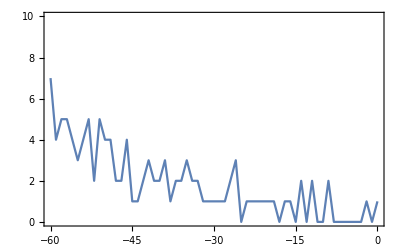

```mathematica
ListPlot[
{
SimonStage1PowerAndErrorRateVSEffect⟦All,{1,2}⟧

},Joined->True,Frame->True,PlotRangePadding->None,PlotRange->{0,10}]
```

```mathematica
Mean[SimonStage1PowerAndErrorRateVSEffect⟦All,{1,3}⟧⟦All,2⟧]//N
```

1.98361

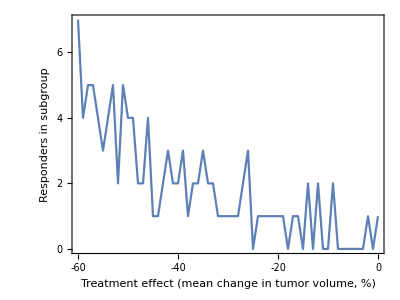

```mathematica
ListPlot[
{
SimonStage1PowerAndErrorRateVSEffect⟦All,{1,2}⟧

},Joined->True,Frame->True,PlotRangePadding->False,PlotRange->{{-60,0},{0,7}},Axes->False,FrameStyle->Directive[Black,Thickness[Medium]],FrameTicks->{{Table[{i,i,{0.02,0}},{i,0,7,1}],None},{Table[{i,i,{0.02,0}},{i,-60,0,10}],None}},FrameLabel->{"Treatment effect\n(mean change in tumor volume, %)","Responders in subgroup"},BaseStyle->{FontFamily->"Arial",FontSize->9},ImagePadding->{{40,10},{60,10}},AspectRatio->3/4,ImageSize->{{500},{170}}]
```

## Simon stage 2 assessment

```mathematica
Stage2ResponsesInGroups[treatmenteffect_]:=Join[
(* responding groups *)Table[GroupOfResponses[Nstage2,treatmenteffect],{NumberOfResponsiveSubtypes}],
(* non-responding groups *)Table[GroupOfResponses[Nstage2,0],{NumberOfNonResponsiveSubtypes}]
]
```

```mathematica
VolumeThresholdForResponse=-30;

SimonStage2Assessment[listofvolumes_]:=
Length[Select[listofvolumes,#<=VolumeThresholdForResponse&]]
```

```mathematica
Map[SimonStage2Assessment,Stage2ResponsesInGroups[-40]]
```

{7,0,0,1,1,1,0,1,1,1}

```mathematica
ManySimonStage2Assessments[numberofsimulations_,treatmenteffect_]:=Table[Map[SimonStage2Assessment,Stage2ResponsesInGroups[treatmenteffect]],{numberofsimulations}]
```

```mathematica
SimonStage2Power[numberofsimulations_,treatmenteffect_]:=Module[{},
SimulatedTrialAssessments=ManySimonStage2Assessments[numberofsimulations,treatmenteffect];

TrialsThatShouldBePositive=SimulatedTrialAssessments⟦All,1;;NumberOfResponsiveSubtypes⟧;


{TrialsThatShouldBePositive}
]
```

```mathematica
SimonStage2PowerAndErrorRateVSEffect=Table[Flatten[{treatmenteffect,SimonStage2Power[1000,treatmenteffect]}],{treatmenteffect,-60,0,1}];
```

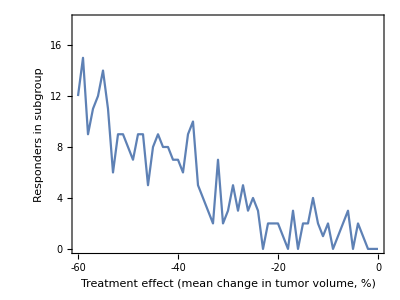

```mathematica
ListPlot[
{
SimonStage2PowerAndErrorRateVSEffect⟦All,{1,2}⟧
},Joined->True,Frame->True,PlotRangePadding->False,PlotRange->{{-60,0},{0,18}},Axes->False,FrameStyle->Directive[Black,Thickness[Medium]],FrameTicks->{{Table[{i,i,{0.02,0}},{i,0,18,2}],None},{Table[{i,i,{0.02,0}},{i,-60,0,10}],None}},FrameLabel->{"Treatment effect\n(mean change in tumor volume, %)","Responders in subgroup"},BaseStyle->{FontFamily->"Arial",FontSize->9},ImagePadding->{{40,10},{60,10}},AspectRatio->3/4,ImageSize->{{500},{170}}]
```

```mathematica
Export[NotebookDirectory[]<>"Simon stage 1 vs stage 2 power.pdf",%,"PDF"]
```